## grupa 1

#### Zad. 1

-2+x+x^2

{{x→-2},{x→1}}

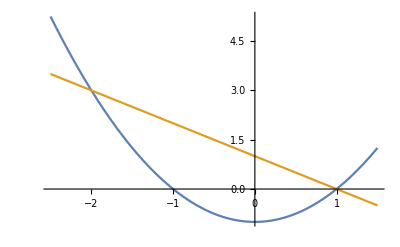

9/2

```mathematica
(x-1)(x+2)//Expand
y1=x^2-1;
y2=1-x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-2.5,1.5}]
Integrate[y2-y1,{x,-2,1}]
```

#### Zad. 2

```mathematica
A1={{1,2,-3},{3,-2,1},{-2,1,3}};
X1={{2},{1},{3}};
B1=A1.X1
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

{{-5},{7},{6}}

{{x→2,y→1,z→3}}

#### Zad. 3

```mathematica
A1={{1,1,-1,-1},{2,1,-1,2},{1,2,-2,1},{-1,-1,2,1}};
Det[A1]
X1={{0},{0},{-2},{0}};
B1=A1.X1
Solve[A1.{{x},{y},{z},{t}}==B1,{x,y,z,t}]
```

6

{{2},{2},{4},{-4}}

{{x→0,y→0,z→-2,t→0}}

## grupa I1

#### Zad. 1

```mathematica
y=2x-x^2;
π Integrate[y,{x,0,2}]
```

(4 π)/3

#### Zad. 2

```mathematica
A1={{1,-1,4},{-4,1,-1},{3,1,2}};
X1={{1},{1},{-1}};
B1=A1.X1
Clear[y];
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

{{-4},{-2},{2}}

{{x→1,y→1,z→-1}}

#### Zad. 3

```mathematica
A1={{2,1,1,2},{1,2,2,1},{1,1,-1,2},{-1,2,-1,1}};
Det[A1]
X1={{0},{3},{0},{0}};
B1=A1.X1
Solve[A1.{{x},{y},{z},{t}}==B1,{x,y,z,t}]
```

-3

{{3},{6},{3},{6}}

{{x→0,y→3,z→0,t→0}}